# KnotTheory` Make.nb

This notebook generates KnotTheory/init.m from the modules in src/ and KnotTheory.zip and KnotTheory.tar.gz from their sources. 
In the future this notebook will supersede the "makefile"; currently the makefile is not operational, but it is kept in the repository because it contains the list of files that go into DTCodes4Knots12To16.tar.gz and DTCodes4Knots12To16.zip which are not yet made by this notebook.
This notebook also contains some testing code.

## The Make Part

Change and execute the following cell to set the path for "trunk" on your system:

```mathematica
Switch["Scott",
"Dror", SetDirectory["C:/drorbn/projects/KnotTheory/svn/trunk"],
"Scott", SetDirectory["~/projects/KnotTheory/trunk"],
"Radmila", SetDirectory["C:\\radmila\\KnotTheory\\trunk"]
]
```

/Users/scott/projects/KnotTheory/trunk

Most times you will not need to edit the follwing variables, so just execute the following cell to initialize them:

```mathematica
PathOf["7z"] := "c:\\Program Files\\7-Zip";
InitSources = ("src/"<>#)& /@ {
"Base.m", "Braids.m", "TubePlot.m", "DrawPD.m", "Data.m", "BraidData.m","Naming.m", "GaussCode.m", "GC2PD.m", "Indiana.m","HyperbolicVolume.m","WikiForm.m", "HOMFLYPT.m", "Kauffman.m", "Kh.m", "MorseLink.m", "DrawMorseLink.m", "ML2PD.m", "AlexanderConway.m", "VogelsAlgorithm.m", "MultivariableAlexander.m", "REngine.m", "TestRMatrix.m", "CJREngine.m", "ColouredJones.m", "HFGenus.m","KTtoLinKnot.m", "ArcPresentation.m", "HFK.m"
};
DistributionFiles= Join[
FileNames["*.m","KnotTheory"],
Select[
FileNames["*",  "KnotTheory"<>$PathnameSeparator<>#&/@{"JavaKh-v1","JavaKh-v2","WikiLink", "KnotAtlas", "scripts", "QuantumGroups", "HFK-Zurich"}, Infinity],
(FileType[#]==File) && StringFreeQ[#,$PathnameSeparator<> "."]&
]
];
```

```mathematica
CreateZip[]:=Module[{},
DeleteFile["KnotTheory.zip"];
Switch[$OperatingSystem,
"Windows",Run[StringJoin[
"\""<>PathOf["7z"]<>"\\7z.exe\" ",
"a -tzip KnotTheory.zip @distribution_files"
]],
"MaxOSX"|_,Run["zip KnotTheory.zip `cat distribution_files`"]
];
]
```

```mathematica
CreateGZ[]:=
Module[{},
DeleteFile["KnotTheory.tar.gz"];
Switch[$OperatingSystem,
"Windows",Block[{},
Run[StringJoin[
"\""<>PathOf["7z"]<>"\\7z.exe\" ",
"a -ttar KnotTheory.tar @distribution_files"
]];
Run["\""<>PathOf["7z"]<>"\\7z.exe\" a -tgzip KnotTheory.tar.gz KnotTheory.tar"];
DeleteFile["KnotTheory.tar"];
],
"MacOSX"|_,Run["tar czvf KnotTheory.tar.gz `cat distribution_files`"]
];
]
```

```mathematica
f=OpenWrite["distribution_files",PageWidth->Infinity];
WriteString[f,StringJoin[#<>"\n"&/@DistributionFiles]];
Close[f];
```

And now the action itself :

```mathematica
lines = StringReplace[#,
"---date---" -> ToString[Date[]]
]& /@ Import["src/System.mm", "Lines"];
lines = Flatten[{
lines,
{
"(* Begin source file "<>#<>"*)\n",
Import[#, "Lines"],
"(* End source file "<>#<>"*)\n\n"
}& /@ InitSources
}];
Export["KnotTheory/init.m", lines, "Lines"];
CreateZip[];
CreateGZ[];
```

```mathematica
Directory[]
```

/Users/scott/projects/KnotTheory/trunk

## The Test Part - Computations

```mathematica
SetAttributes[Assert, HoldAll];
Assert[fact_] := Module[
{result=fact},
If[result===True,
True,
Print[
StringTake[ToString[Hold[fact]], {6,-2}],
" yields ", fact]
]
];
```

```mathematica
<< KnotTheory`
```

Loading KnotTheory` version of March 22, 2011, 21:10:4.67737.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
Assert[Jones[Link["L11n458"]][q] == Jones[DTCode[Link["L11n458"]]][q]]
```

True

```mathematica
Assert[Kh[PD[Knot[3,1]]][q,t]== 1/q^3+1/q+1/(q^9 t^3)+1/(q^5 t^2)]
```

True

```mathematica
Assert[Kh[PD[Knot[4,1]],Program->"FastKh"][q,t]==1/q+q+1/(q^5 t^2)+1/(q t)+q t+q^5 t^2]
```

True

```mathematica
Assert[Last[Kh[TorusKnot[6,5], Modulus -> Null][q,t]] == q^39 t^12 ZMod[2,5]]
```

True

```mathematica
Assert[Alexander["K11a44",2][t] === {1-t+t^2}]
```

True

```mathematica
Assert[
Alexander["10_99",#][t]& /@ {1,2} === {{1-4 t+10 t^2-16 t^3+19 t^4-16 t^5+10 t^6-4 t^7+t^8},{1-2 t+3 t^2-2 t^3+t^4}}
]
```

True

```mathematica
Assert[
ArcPresentation["K11n11"] === ArcPresentation[{12,2},{1,10},{3,9},{5,11},{9,12},{4,8},{2,5},{11,7},{8,6},{7,4},{10,3},{6,1}]
]
```

True

```mathematica
Assert[
BR[ArcPresentation[
{12,2},{1,10},{3,9},{5,11},{9,12},{4,8},{2,5},{11,7},{8,6},{7,4},{10,3},{6,1}]
] === BR[4,{-1,2,3,3,-2,-1,-2,-1,2,3,3,3,2}]
]
```

True

```mathematica
Assert[(HFKHat[Knot[8,19]][t,m] /. m -> 1/t) == 4/t^3+1/t^2]
```

True

```mathematica
Assert[(HFKHat[BR[Knot[8,19]]][t,m] /. m -> 1/t) == 4/t^3+1/t^2]
```

1     4    1
Hold[(HFKHat[BR[Knot[8, 19]]][t, m] /. m -> -) == -- + --]
                                            t      3    2
                                                  t     yields $Failed[t,1/t]==4/t^3+1/t^2

```mathematica
Assert[(Plus@@ (AlternatingQ /@ AllKnots[8])) ==  3False+18 True]
```

True

```mathematica
Assert[AlternatingQ[Knot[0,1]] == True]
```

True

```mathematica
Assert[
MultivariableAlexander[Link["L7a7"]][t]== MultivariableAlexander[PD[Link["L7a7"]]][t]
]
```

True

```mathematica
Flip[X[i_,j_,k_,l_]] := If[l==j+1 || j-l>1, X[j,k,l,i], X[l,i,j,k]];
VassilievCube[{}, pdcomb_] := pdcomb;
VassilievCube[{i_, rest___}, pdcomb_] := VassilievCube[{rest},
Expand[pdcomb-(pdcomb /. pd_PD :> MapAt[Flip, pd, i])]
]
```

```mathematica
Assert[Equal[
Series[
VassilievCube[{1,2,5,7}, PD[#]]
/. pd_PD :> MultivariableAlexander[pd][t] /. t[i_] -> E^(h x[i]),
{h, 0,2}
]& /@AllLinks[7],
{O[h]^3,O[h]^3,O[h]^3,O[h]^3,O[h]^3,O[h]^3,O[h]^3,O[h]^3,O[h]^3}
]]
```

True

```mathematica
Assert[Equal[
Series[
VassilievCube[{1,2,5,7}, PD[Link[7, Alternating, 1]]]
/. pd_PD :> MultivariableAlexander[pd, Program -> "MVA1"][t] /. t[i_] -> E^(h x[i]),
{h, 0,2}
],
-2 x[1] h+(-2 x[1]^2-x[1] x[2]) h^2+O[h]^3
]]
```

True

## The Test Part - Graphics

```mathematica
TubePlot[TorusKnot[4,3]] // Show
```

-Graphics3D-

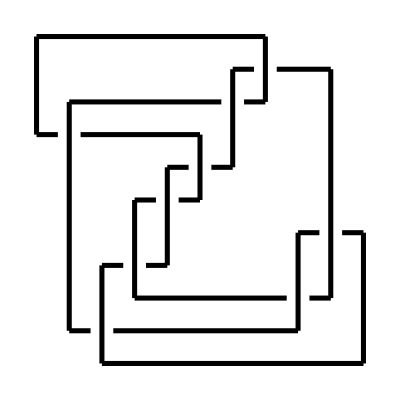

```mathematica
Draw[ArcPresentation[Knot[9,17]]]
```